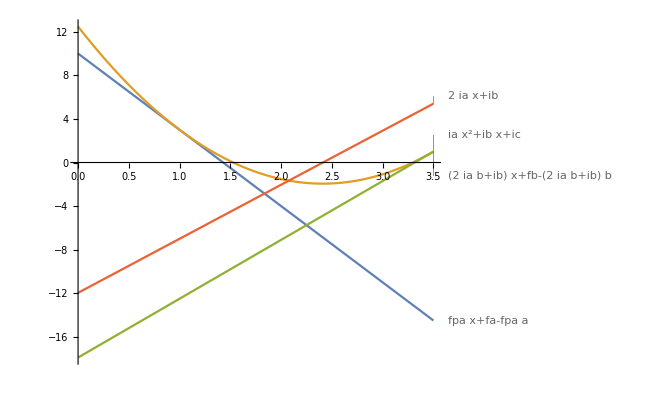

```mathematica
Block[{fa =  3, fb =1, fpa = -7, a = 1, b = 3.5},
Block[{
ia =(fb-fpa*b-fa+fpa*a) / (b*b -2*a*b+a*a),
ib=fpa-2*a*ia,
ic=fa-ia*a*a-ib*a},
Plot[{fpa*x+fa - fpa*a,
ia*x^2+ib*x+ic,
(2*ia*b+ib)*x+fb-(2*ia*b+ib)*b,
2*ia*x+ib},{x,0, 3.5},PlotLabels->"Expressions"]]]
```

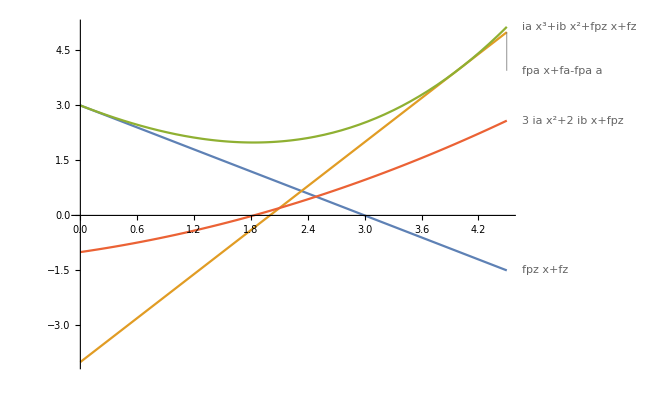

```mathematica
Block[{fz =  3, fpz =-1, fa = 4, fpa = 2, a = 4},
Block[{
ia =-2 * (fa-fpz*a-fz-a*(fpa-fpz)/2) / a^3,
ib=(fpa-fpz-3*ia*a^2)/(2*a)},
Plot[{fpz*x+fz,
fpa*x+fa - fpa*a,
ia*x^3+ib*x^2+fpz*x+fz,
3*ia*x^2+2*ib*x+fpz},{x,0, 4.5},PlotLabels->"Expressions"]]]
```